## Energia de deformação para material hiper elastico

```mathematica
U=C10 (I1[F]-3)+C01(I2[F]-3)+1/D1(J[F]-1)^2
subst={
I3C[F]->Det[Transpose[F].F],
IC[F]->Tr[Transpose[F].F],
I2C[F]->(1/2)(Tr[Transpose[F].F]^2-(Tr[Transpose[F].F.Transpose[F].F]) ) 
}
substgrad={
D[I3C[F],F]->2 (Det[F])^(2) Inverse[Transpose[F]],
D[IC[F],F]->2 F,
D[I2C[F],F]->(2Tr[ Transpose[F].F]F-2 F.Transpose[F].F)
}
I1[F_]=I3C[F]^(-1/3) IC[F]
I2[F_]=I3C[F]^(-1/3) I2C[F]
J[F_]=I3C[F]^(1/2)
S[F_]=D[U,F]/.substgrad/.subst/.{C01->0}
```

C01 (-3+I2C[F]/I3C[F]^(1/3))+(-1+√I3C[F])^2/D1+C10 (-3+IC[F]/I3C[F]^(1/3))

{I3C[F]→Det[Transpose[F].F],IC[F]→Tr[Transpose[F].F],I2C[F]→1/2 (Tr[Transpose[F].F]^2-Tr[Transpose[F].F.Transpose[F].F])}

{I3C'[F]→2 Det[F]^2 Inverse[Transpose[F]],IC'[F]→2 F,I2C'[F]→-2 F.Transpose[F].F+2 F Tr[Transpose[F].F]}

IC[F]/I3C[F]^(1/3)

I2C[F]/I3C[F]^(1/3)

√I3C[F]

(2 Det[F]^2 (-1+√Det[Transpose[F].F]) Inverse[Transpose[F]])/(D1 √Det[Transpose[F].F])+C10 ((2 F)/Det[Transpose[F].F]^(1/3)-(2 Det[F]^2 Inverse[Transpose[F]] Tr[Transpose[F].F])/(3 Det[Transpose[F].F]^(4/3)))

```mathematica
D[I2[F],F]/.substgrad/.subst /.F->IdentityMatrix[3]
```

{{2,0,0},{0,2,0},{0,0,2}}

```mathematica
RandomReal[{-0.1,0.1},{3,3}]
```

{{-0.0423137,0.0263573,0.0475519},{-0.00617083,0.0366431,-0.0384646},{-0.0375689,0.047064,0.0334813}}

```mathematica
I2[F]/.subst/.substgrad
```

(Tr[Transpose[F].F]^2-Tr[Transpose[F].F.Transpose[F].F])/(2 Det[Transpose[F].F]^(1/3))

```mathematica
FuncAlfa[alfa_]=I2[F]/.subst/.F->IdentityMatrix[3]+alfa RandomReal[{-0.1,0.1},{3,3}];
```

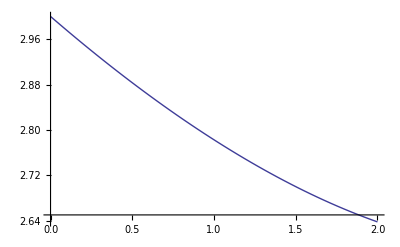

3

-0.249124

```mathematica
Plot[FuncAlfa[alfa],{alfa,0,2}]
FuncAlfa[0]
D[FuncAlfa[alfa],alfa]/.alfa->0
```

```mathematica
D[I2C[F],F]/.substgrad/.F->IdentityMatrix[3]
```

{{4,0,0},{0,4,0},{0,0,4}}

```mathematica
S[IdentityMatrix[3]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
U/.subst/.F->IdentityMatrix[3]
```

0

```mathematica
I2[F]/.subst/.F->IdentityMatrix[3]
```

3

```mathematica
(2Tr[ Transpose[F].F]F+2 F.Transpose[F].F)/.F->IdentityMatrix[3]
```

{{8,0,0},{0,8,0},{0,0,8}}

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
D[I2C[F],F]
```

I2C'[F]